# PJ41 Io Color Match

Setup:
	Download basemap Io_Galileo _SSI _Global _Mosaic _ClrMerge _ 32ppd.jpg from USGS
	Render JunoCam EQR Map of Io registered to basemap (Using blenderBatch-eqrmaps.sh and startup_file=JunocamLibraryJunoSceneMap32ppdC.blend
	
Method: find matrix that converts JunoCam colors to basemap.
Uses equirectangular map projection of JunoCam image. Alternative approach would be to render basemap as though imaged from JunoCam.

```mathematica
$Version
```

12.0.0 for Mac OS X x86 (64-bit) (April 7, 2019)

```mathematica
Now
```

Wed 4 May 2022 18:32:09GMT-7.

## Import Io basemap and JunoCam source image

```mathematica
eqrBaseImg=Import["/Users/bswift/Downloads/Io_Galileo_SSI_Global_Mosaic_ClrMerge_32ppd.jpg"];
```

```mathematica
img=Import["/Volumes/Macintosh HD/Users/bswift/Downloads/junoDirs/PJ41io/zMP41_05_04k_1.exr"]; (* Using PJ41_05 image because it has largest amount of illuminated area away from terminator *)
```

```mathematica
img//ImageDimensions
```

{11520,5760}

```mathematica
11520/360 (* pixels per degree *)
```

32

## Resize Images

Large 32 pixel-per-degree maps are resized to 1 pixel-per-degree to be more manageable data volume and to be closer to intrinsic JunoCam resolution. Images are blurred prior to scaling so basemap resolution characteristic closer to JunoCam image.

```mathematica
newDimensions=360{1,1/2}
```

{360,180}

#### Resize JunoCam Source Image

```mathematica
imgDefaultScaled=ImageResize[img,newDimensions]
```

-Graphics-

```mathematica
imgGFScaled=ImageResize[GaussianFilter[img,96],newDimensions,Resampling->"Nearest"(*"Linear"*)](* Choosing a level of blurring that starts to show difference with wrt non-blurred resized. Idea is that when this level of blur is applied to basemap, it will give the basemaps similar resolution characteristic to JunoCam image. *)
```

-Graphics-

```mathematica
10ImageDifference[imgDefaultScaled,imgGFScaled]
```

-Graphics-

```mathematica
imgScaled=imgGFScaled;
```

#### Resize Basemap

```mathematica
eqrBaseLinearImg=srgb2linearImage[eqrBaseImg];
```

```mathematica
resizedFromLinearImage=linear2srgbImage[ImageResize[GaussianFilter[eqrBaseLinearImg,96],newDimensions,Resampling->"Nearest"(*"Linear"*)]](* Very little difference between Resampling->"Nearest" vs "Linear" *)
```

-Graphics-

```mathematica
resizedFromSRGB=ImageResize[GaussianFilter[eqrBaseImg,96],newDimensions,Resampling->"Nearest"(*"Linear"*)]
```

-Graphics-

```mathematica
10ImageDifference[resizedFromLinearImage,resizedFromSRGB](* some but not huge impact resizing in linear vs sRGB *)
```

-Graphics-

```mathematica
eqrBaseDefaultScaledImg=ImageResize[eqrBaseImg,newDimensions](* resize basemap without blur has resolution characteristic very different than JunoCam source image *)
```

-Graphics-

```mathematica
eqrBaseImgScaled=resizedFromLinearImage
```

-Graphics-

## Select Region For Matching

Selecting bright-ish region of JunoCam source image (away from terminator and limb) to use for matching.
Additional refinement would be to apply incidence angle illumination correction.

```mathematica
regionMask=Erosion[FillingTransform[binarize3ChannelAllGreaterThanThreshold[imgScaled,.05]],DiskMatrix[15]](* using GaussianFilter scaled image had little impact regionMask *)
```

-Graphics-

```mathematica
(1-regionMask )imgScaled (* what is beign excluded from match *)
```

-Graphics-

```mathematica
linear2srgbImage[imgScaled]
```

-Graphics-

```mathematica
{linearSourceImage,srgbTargetImage}=regionMask RemoveAlphaChannel[#]&/@{imgScaled,eqrBaseImgScaled}
```

{-Graphics-,-Graphics-}

```mathematica
imageInfo/@{linearSourceImage,srgbTargetImage}
```

{<|Channels→3,ColorSpace→RGB,DataRange→{0.,1.},DataType→Real32,Dimensions→{3,180,360},SampleDepth→32,Transparency→False,Min→{0.,0.,0.},Max→{0.464731,0.380492,0.363011},Mean→{0.0323801,0.0251578,0.0228769},Median→{0.,0.,0.},StandardDeviation→{0.0930395,0.0730336,0.0666993}|>,<|Channels→3,ColorSpace→RGB,DataRange→{0.,1.},DataType→Real32,Dimensions→{180,360,3},SampleDepth→32,Transparency→False,Min→{0.,0.,0.},Max→{0.780325,0.707935,0.643243},Mean→{0.0718387,0.0606028,0.0401165},Median→{0.,0.,0.},StandardDeviation→{0.199958,0.168837,0.113282}|>}

## Matching

### Extract pixels to be used in matching optimzation

```mathematica
{linearSourceAll,srgbTargetAll,maskAsIntsAll}=Map[Flatten[ImageData[#],1]&,{linearSourceImage,srgbTargetImage,regionMask}];(* convert source target and mask from images to 1-d vectors of pixels *)
```

```mathematica
Dimensions/@{linearSourceAll,srgbTargetAll,maskAsIntsAll}
```

{{64800,3},{64800,3},{64800}}

```mathematica
Counts[maskAsIntsAll]
```

<|0→57345,1→7455|>

```mathematica
linearSource=Pick[linearSourceAll,maskAsIntsAll,1]; (* select source image pixels based on mask *)
```

```mathematica
linearSource//Dimensions
```

{7455,3}

```mathematica
srgbTarget=Pick[srgbTargetAll,maskAsIntsAll,1];(* select corresponding target/basemap image pixels based on same mask *)
```

```mathematica
Dimensions/@{linearSource,srgbTarget}
```

{{7455,3},{7455,3}}

```mathematica
(*targetXYZColor=Map[XYZColor[RGBColor[#]]&,srgbTarget];*)(* convert target/basemap sRGB pixels to XYZ. Needs MM13 *)
```

```mathematica
targetXYZColor=Map[ColorConvert[RGBColor[#],"XYZ"]&,srgbTarget];(* convert target/basemap sRGB pixels to XYZ  *)(* MM12 *)
```

```mathematica
Max[Norm/@((List@@@ColorConvert[targetXYZColor,"RGB"])-srgbTarget)] (* targetXYZColor convert back to srgbTarget losslessly *)
```

1.13656×10^-6

```mathematica
Dimensions/@{linearSource,targetXYZColor}
```

{{7455,3},{7455}}

```mathematica
Length[Cases[srgbTarget,{0.,0.,0.}]](* confirming no 0s in target *)
```

0

```mathematica
Length[Cases[linearSource,{0.,0.,0.}]](* confirming no 0s in source *)
```

0

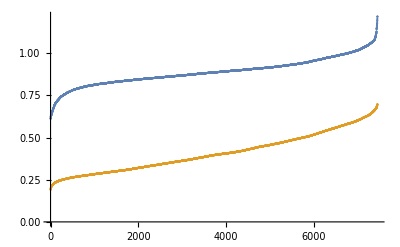

```mathematica
ListPlot[{Sort[Norm/@srgbTarget],Sort[Norm/@linearSource]},PlotRange->All]
```

### Define Color Matching Model

```mathematica
(* modifed from Mars2020EDLProcessingV2.nb modelW11 - IDT assuming D65 illuminant. *)
modelW12=.;
modelW12["params"]:={β1,β2,β3,β4,β5,β6,β7,β8,β9};
modelW12["constraints"]:={};
modelW12["initialPoints"]:={{1.,0.,0.,1.,0.,0. 
,0.,0.,1.}};
modelW12["size"]:=Length[linearSource];
modelW12["matrix"]:={{β1,β2,β7}
,{β3,β4,β8}
,{β5,β6,β9}
};

modelW12[
β1_?NumericQ,β2_,β3_,β4_,β5_,β6_,β7_,β8_,β9_ (* IDT *)
]:=
Block[
{
},
RootMeanSquare[
MapThread[
ColorDistance[#1,#2,DistanceFunction->"CIE2000" ]&(* would be nice if ColorDistance could be evaluated symbolically. *)
,{(XYZColor[
({{β1,β2,β7}
,{β3,β4,β8}
,{β5,β6,β9}
}.{ #⟦1⟧
, #⟦2⟧
, #⟦3⟧
})⟦1;;3⟧
]&/@linearSource)
,targetXYZColor}]
]
]
```

```mathematica
modelToOpt=modelW12
```

modelW12

```mathematica
AbsoluteTiming[
modelToOpt@@(modelToOpt["initialPoints"]⟦1⟧)
](* test evaluation of model *)
```

{0.31145,0.321423}

### NMinimize optimization

```mathematica
logMessagePeriod=Quantity[30.,"Seconds"];
lastStepCount=0;
lastEvalCount=0;
stepCount=0;
evalCount=0;

paramsToOptString=ToString[modelToOpt["params"]];Print["model size ",modelToOpt["size"]];
Print["paramsToOptimize ",modelToOpt["params"]];Print["initialPoints = ", modelToOpt["initialPoints"]];
Print["Constraints ",modelToOpt["constraints"]];

dim=Length[modelToOpt["params"]];
Print["dim ",dim];

Print["Start Time ",lastTime=(optStartTime=Now)];

AbsoluteTiming[
BlockRandom[SeedRandom[7654];
optResultsNMinimize=NMinimize(*NMaximize*)[
(* function and constraints *)
Join[{
cs=( modelToOpt@@modelToOpt["params"])
},modelToOpt["constraints"]]

,modelToOpt["params"]


(* options *)
(*,Method->{"NelderMead"}*)
,Method->{"NelderMead"
,"PostProcess"-> False
,"ReflectRatio"->1,"ExpandRatio"-> 1+2/dim,"ContractRatio"-> 3/4-1/(2 dim),"ShrinkRatio"-> 1-1/dim(* These parameters are supposed to help when working with a large number of dimensions. They are mentiond at https://mathematica.stackexchange.com/questions/4700/shaving-the-last-50-ms-off-nminimize/4877#4877 *)
(*,"ReflectRatio"->2.,"ExpandRatio"-> 2.,"ContractRatio"-> .95,"ShrinkRatio"-> .95 (* from example in tutorial/ConstrainedOptimizationGlobalNumerical  *)*)
,"InitialPoints"-> modelToOpt["initialPoints"]
} 
,StepMonitor:> 
(stepCount++;If[(msgTime=DateDifference[lastTime,curTime=Now,"Minute"])> logMessagePeriod||Mod[stepCount,500]==1
,
lastSoln=modelToOpt["params"];
Print[{"StepRate=",(stepCount-lastStepCount)/msgTime
,"EvalRate=",(evalCount-lastEvalCount)/msgTime
,"Steps Evals" ,stepCount,evalCount," SPREAD",cs
,paramsToOptString
,modelToOpt["params"]
,lastTime=curTime,{"Elapsed time", DateDifference[optStartTime,curTime,"Minute"]}
}
];
(*Print[Stack[_]];*)
lastStepCount=stepCount;
lastEvalCount=evalCount;
]
)
,EvaluationMonitor :> evalCount++
(*,AccuracyGoal->6+1
,PrecisionGoal->4+1*)
,MaxIterations->4 12000
]
]
]
```

model size 7455

paramsToOptimize {β1,β2,β3,β4,β5,β6,β7,β8,β9}

initialPoints = {{1.,0.,0.,1.,0.,0.,0.,0.,1.}}

Constraints {}

dim 9

Start Time Wed 4 May 2022 18:35:14GMT-7.

{StepRate=,17.8348 per minute,EvalRate=,178.348 per minute,Steps Evals,1,10, SPREAD,0.194186,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.469283,0.998909,0.9254,0.238681,-0.0659171,0.761509,0.469057,0.857835,0.633737},Wed 4 May 2022 18:35:17GMT-7.,{Elapsed time,0.0560701 min}}

{StepRate=,83.8581 per minute,EvalRate=,140.414 per minute,Steps Evals,44,82, SPREAD,0.134092,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.636063,0.613341,0.690266,0.331227,-0.00168191,0.494303,0.363207,0.677788,0.563923},Wed 4 May 2022 18:35:48GMT-7.,{Elapsed time,0.568841 min}}

{StepRate=,70.2105 per minute,EvalRate=,124.819 per minute,Steps Evals,80,146, SPREAD,0.0843393,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.876476,0.122764,0.392053,0.615606,0.121378,0.0178296,0.244121,0.341261,0.389456},Wed 4 May 2022 18:36:19GMT-7.,{Elapsed time,1.08158 min}}

{StepRate=,80.2128 per minute,EvalRate=,140.861 per minute,Steps Evals,121,218, SPREAD,0.071845,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.503452,0.461023,0.309066,0.304373,-0.215421,0.372897,0.131396,0.569364,0.457963},Wed 4 May 2022 18:36:50GMT-7.,{Elapsed time,1.59273 min}}

{StepRate=,94.9187 per minute,EvalRate=,158.198 per minute,Steps Evals,169,298, SPREAD,0.0699326,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.554161,0.332011,0.330502,0.353067,-0.163785,0.292047,0.217425,0.491313,0.450879},Wed 4 May 2022 18:37:20GMT-7.,{Elapsed time,2.09842 min}}

{StepRate=,119.383 per minute,EvalRate=,161.167 per minute,Steps Evals,229,379, SPREAD,0.068167,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.551801,0.161911,0.369501,0.386404,-0.15073,0.237266,0.381082,0.380285,0.47427},Wed 4 May 2022 18:37:50GMT-7.,{Elapsed time,2.60101 min}}

{StepRate=,116.88 per minute,EvalRate=,160.462 per minute,Steps Evals,288,460, SPREAD,0.0678031,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.590018,0.0930233,0.376108,0.440703,-0.154774,0.213392,0.409785,0.318353,0.514854},Wed 4 May 2022 18:38:20GMT-7.,{Elapsed time,3.1058 min}}

{StepRate=,111.182 per minute,EvalRate=,158.831 per minute,Steps Evals,344,540, SPREAD,0.0674421,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.609368,0.0963667,0.374063,0.477376,-0.26379,0.267151,0.363569,0.265116,0.610337},Wed 4 May 2022 18:38:51GMT-7.,{Elapsed time,3.60948 min}}

{StepRate=,111.525 per minute,EvalRate=,154.569 per minute,Steps Evals,401,619, SPREAD,0.0673249,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.6446,0.0840993,0.376976,0.509094,-0.306115,0.28078,0.335558,0.233628,0.655239},Wed 4 May 2022 18:39:21GMT-7.,{Elapsed time,4.12058 min}}

{StepRate=,99.6929 per minute,EvalRate=,153.527 per minute,Steps Evals,451,696, SPREAD,0.0671564,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.685662,0.0374921,0.425358,0.460849,-0.321124,0.308597,0.33001,0.219517,0.650167},Wed 4 May 2022 18:39:51GMT-7.,{Elapsed time,4.62212 min}}

{StepRate=,97.9918 per minute,EvalRate=,149.987 per minute,Steps Evals,500,771, SPREAD,0.0664218,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.938604,-0.310227,0.625589,0.18829,-0.233931,0.329366,0.34911,0.229554,0.499044},Wed 4 May 2022 18:40:21GMT-7.,{Elapsed time,5.12216 min}}

{StepRate=,50.8803 per minute,EvalRate=,101.761 per minute,Steps Evals,501,773, SPREAD,0.0664062,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.931148,-0.342404,0.644671,0.190861,-0.221255,0.315255,0.395775,0.201993,0.493043},Wed 4 May 2022 18:40:22GMT-7.,{Elapsed time,5.14181 min}}

{StepRate=,99.0246 per minute,EvalRate=,152.498 per minute,Steps Evals,551,850, SPREAD,0.0659461,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.24569,-0.748748,0.946095,-0.245549,-0.133085,0.400277,0.392251,0.247366,0.272268},Wed 4 May 2022 18:40:53GMT-7.,{Elapsed time,5.64674 min}}

{StepRate=,82.1229 per minute,EvalRate=,154.469 per minute,Steps Evals,593,929, SPREAD,0.0659355,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.25788,-0.761523,0.95694,-0.250418,-0.146097,0.408691,0.391185,0.239681,0.28069},Wed 4 May 2022 18:41:23GMT-7.,{Elapsed time,6.15817 min}}

{StepRate=,95.2447 per minute,EvalRate=,154.773 per minute,Steps Evals,641,1007, SPREAD,0.0659344,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.26006,-0.768192,0.958305,-0.251792,-0.143719,0.406558,0.394819,0.238922,0.279167},Wed 4 May 2022 18:41:54GMT-7.,{Elapsed time,6.66213 min}}

{StepRate=,113.897 per minute,EvalRate=,157.099 per minute,Steps Evals,699,1087, SPREAD,0.065932,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.26254,-0.77651,0.960651,-0.262519,-0.147223,0.409665,0.400877,0.247911,0.281163},Wed 4 May 2022 18:42:24GMT-7.,{Elapsed time,7.17136 min}}

{StepRate=,90.8961 per minute,EvalRate=,152.152 per minute,Steps Evals,745,1164, SPREAD,0.0659202,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.25673,-0.811405,0.951479,-0.287763,-0.149444,0.402503,0.44749,0.288435,0.292446},Wed 4 May 2022 18:42:55GMT-7.,{Elapsed time,7.67744 min}}

{StepRate=,95.8243 per minute,EvalRate=,155.714 per minute,Steps Evals,793,1242, SPREAD,0.0659017,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.25483,-0.934271,0.948346,-0.398998,-0.168961,0.400539,0.586565,0.416248,0.322425},Wed 4 May 2022 18:43:25GMT-7.,{Elapsed time,8.17835 min}}

{StepRate=,90.1782 per minute,EvalRate=,152.911 per minute,Steps Evals,839,1320, SPREAD,0.065901,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.25802,-0.951222,0.950923,-0.415247,-0.167213,0.399685,0.599875,0.42976,0.320011},Wed 4 May 2022 18:43:55GMT-7.,{Elapsed time,8.68845 min}}

{StepRate=,103.931 per minute,EvalRate=,155.896 per minute,Steps Evals,891,1398, SPREAD,0.0659008,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.25767,-0.95375,0.950488,-0.417642,-0.167508,0.399443,0.60342,0.433353,0.321026},Wed 4 May 2022 18:44:25GMT-7.,{Elapsed time,9.18879 min}}

{StepRate=,111.822 per minute,EvalRate=,153.02 per minute,Steps Evals,948,1476, SPREAD,0.0659005,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.25809,-0.957998,0.951022,-0.421918,-0.167863,0.399397,0.607329,0.437065,0.321396},Wed 4 May 2022 18:44:56GMT-7.,{Elapsed time,9.69852 min}}

{StepRate=,98.7564 per minute,EvalRate=,156.035 per minute,Steps Evals,998,1555, SPREAD,0.0658997,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.25828,-0.960397,0.950582,-0.422798,-0.165918,0.397075,0.609798,0.438752,0.32099},Wed 4 May 2022 18:45:26GMT-7.,{Elapsed time,10.2048 min}}

{StepRate=,81.2331 per minute,EvalRate=,135.388 per minute,Steps Evals,1001,1560, SPREAD,0.0658995,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.25921,-0.956778,0.951368,-0.418928,-0.167348,0.398407,0.604366,0.43324,0.321746},Wed 4 May 2022 18:45:28GMT-7.,{Elapsed time,10.2418 min}}

{StepRate=,92.236 per minute,EvalRate=,156.997 per minute,Steps Evals,1048,1640, SPREAD,0.065894,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.25405,-0.941505,0.948499,-0.407679,-0.166281,0.39397,0.594645,0.424539,0.324438},Wed 4 May 2022 18:45:59GMT-7.,{Elapsed time,10.7513 min}}

{StepRate=,87.7704 per minute,EvalRate=,155.593 per minute,Steps Evals,1092,1718, SPREAD,0.0658592,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.23892,-0.918222,0.939334,-0.393933,-0.156833,0.362713,0.589757,0.42194,0.344874},Wed 4 May 2022 18:46:29GMT-7.,{Elapsed time,11.2526 min}}

{StepRate=,93.6843 per minute,EvalRate=,154.189 per minute,Steps Evals,1140,1797, SPREAD,0.0656981,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.20998,-0.849715,0.915957,-0.347898,-0.124567,0.202503,0.557962,0.407276,0.476412},Wed 4 May 2022 18:47:00GMT-7.,{Elapsed time,11.765 min}}

{StepRate=,88.8371 per minute,EvalRate=,150.036 per minute,Steps Evals,1185,1873, SPREAD,0.0652143,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.34762,-1.41085,1.06836,-0.977768,-0.0364129,-0.292559,0.979545,0.885868,0.904608},Wed 4 May 2022 18:47:30GMT-7.,{Elapsed time,12.2715 min}}

{StepRate=,101.679 per minute,EvalRate=,147.534 per minute,Steps Evals,1236,1947, SPREAD,0.0650563,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.45129,-1.69395,1.16753,-1.25588,0.0539647,-0.620678,1.13959,1.04447,1.12751},Wed 4 May 2022 18:48:00GMT-7.,{Elapsed time,12.7731 min}}

{StepRate=,86.6862 per minute,EvalRate=,147.761 per minute,Steps Evals,1280,2022, SPREAD,0.0650487,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.48661,-1.78153,1.20384,-1.3442,0.0858128,-0.686789,1.18737,1.09193,1.15606},Wed 4 May 2022 18:48:31GMT-7.,{Elapsed time,13.2807 min}}

{StepRate=,83.0942 per minute,EvalRate=,150.361 per minute,Steps Evals,1322,2098, SPREAD,0.0650483,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.49484,-1.79973,1.21001,-1.3607,0.0855487,-0.693474,1.19667,1.10217,1.16463},Wed 4 May 2022 18:49:01GMT-7.,{Elapsed time,13.7861 min}}

{StepRate=,89.6817 per minute,EvalRate=,153.455 per minute,Steps Evals,1367,2175, SPREAD,0.0650482,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{1.49045,-1.79369,1.20593,-1.35438,0.0835496,-0.689237,1.19613,1.10093,1.16277},Wed 4 May 2022 18:49:31GMT-7.,{Elapsed time,14.2879 min}}

{868.201,{0.0650482,{β1→1.49128,β2→-1.79507,β3→1.20657,β4→-1.35542,β5→0.0840948,β6→-0.69009,β7→1.19642,β8→1.10108,β9→1.1629}}}

```mathematica
{449.749488,{0.06504822763354264,{β1->1.491292359181276,β2->-1.7960376853004212,β3->1.2067447706083325,β4->-1.356057099050521,β5->0.0828220113732471,β6->-0.6855427916023635,β7->1.1972660315084747,β8->1.1014066932712097,β9->1.159563010278271}}}
(* 
"model size "7455
"paramsToOptimize "{β1,β2,β3,β4,β5,β6,β7,β8,β9}
"initialPoints = "{{1.,0.,0.,1.,0.,0.,0.,0.,1.}}
"Constraints "{}
"dim "9

Method->{"NelderMead"
,"PostProcess"-> False
,"ReflectRatio"->1,"ExpandRatio"-> 1+2/dim,"ContractRatio"-> 3/4-1/(2 dim),"ShrinkRatio"-> 1-1/dim
}
{"StepRate=",Quantity[177.30737827798674, 1/("Minutes")],"EvalRate=",Quantity[272.933829484092, 1/("Minutes")],"Steps Evals",1254,1940," SPREAD",0.06505132150479297,"{β1, β2, β3, β4, β5, β6, β7, β8, β9}",{1.4977258230191923,-1.8571307886303856,1.2144166226369255,-1.411834359787486,0.09041050252466226,-0.7119320504453279,1.2553935878821436,1.1516803432841816,1.178131908893665},DateObject[{2022,5,4,15,27,46.788908`8.422717885983557},"Instant","Gregorian",-7.],{"Elapsed time",Quantity[6.997241833333334, "Minutes"]}}

{449.749488,{0.06504822763354264,{β1->1.491292359181276,β2->-1.7960376853004212,β3->1.2067447706083325,β4->-1.356057099050521,β5->0.0828220113732471,β6->-0.6855427916023635,β7->1.1972660315084747,β8->1.1014066932712097,β9->1.159563010278271}}}
*)
```

{449.749,{0.0650482,{β1→1.49129,β2→-1.79604,β3→1.20674,β4→-1.35606,β5→0.082822,β6→-0.685543,β7→1.19727,β8→1.10141,β9→1.15956}}}

```mathematica
{301.134477,{0.06585012259832367,{β1->1.2839820746142772,β2->-0.9439895664219697,β3->0.978976850674999,β4->-0.41680855299265185,β5->-0.14601951885752176,β6->0.36941049134944337,β7->0.5550499796453566,β8->0.3917314509744998,β9->0.32329793034250204}}};(* 9 parameter "Tue 3 May 2022 16:54:47" *)
```

### FindMinimum Optimization

```mathematica
logMessagePeriod=Quantity[30.,"Seconds"];
lastStepCount=0;
lastEvalCount=0;
stepCount=0;
evalCount=0;

paramsToOptString=ToString[modelToOpt["params"]];Print["model size ",modelToOpt["size"]];
Print["paramsToOptimize ",modelToOpt["params"]];Print["initialPoints = ", modelToOpt["initialPoints"]];
(*Print["Constraints ",modelToOpt["constraints"]];*)

dim=Length[modelToOpt["params"]];
Print["dim ",dim];

Print["Start Time ",lastTime=(optStartTime=Now)];

AbsoluteTiming[
BlockRandom[SeedRandom[7654];
optResultsFindMinimum=FindMinimum[
(* function and constraints *)
(cs= modelToOpt@@modelToOpt["params"])
,{modelToOpt["params"],modelToOpt["initialPoints"][[1]]}ᵀ
,Method->"PrincipalAxis" 
,StepMonitor:> 
(stepCount++;If[(msgTime=DateDifference[lastTime,curTime=Now,"Minute"])> logMessagePeriod||Mod[stepCount,500]==1
,
lastSoln=modelToOpt["params"];
Print[{"StepRate=",(stepCount-lastStepCount)/msgTime
,"EvalRate=",(evalCount-lastEvalCount)/msgTime
,"Steps Evals" ,stepCount,evalCount," SPREAD",cs
,paramsToOptString
,modelToOpt["params"]
,lastTime=curTime,{"Elapsed time", DateDifference[optStartTime,curTime,"Minute"]}
}
];
(*Print[Stack[_]];*)
lastStepCount=stepCount;
lastEvalCount=evalCount;
]
)
,EvaluationMonitor :> evalCount++
(*,AccuracyGoal->6+1
,PrecisionGoal->4+1*)
,MaxIterations->4 12000
]
]
]
```

model size 7455

paramsToOptimize {β1,β2,β3,β4,β5,β6,β7,β8,β9}

initialPoints = {{1.,0.,0.,1.,0.,0.,0.,0.,1.}}

dim 9

Start Time Wed 4 May 2022 18:49:43GMT-7.

{StepRate=,0.840061 per minute,EvalRate=,158.772 per minute,Steps Evals,1,189, SPREAD,0.0816745,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.760332,0.00273602,0.0576836,0.992255,-0.428434,-0.00461352,0.121066,0.00776505,1.04027},Wed 4 May 2022 18:50:54GMT-7.,{Elapsed time,1.19039 min}}

{StepRate=,1.62136 per minute,EvalRate=,154.029 per minute,Steps Evals,2,284, SPREAD,0.0762884,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.76247,0.0438078,0.122911,0.968016,-0.374765,0.00455989,0.182252,0.0726703,1.06469},Wed 4 May 2022 18:51:31GMT-7.,{Elapsed time,1.80715 min}}

{StepRate=,1.51573 per minute,EvalRate=,153.089 per minute,Steps Evals,3,385, SPREAD,0.0729812,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.762162,0.0715681,0.15476,0.94599,-0.393761,0.0131037,0.242478,0.121847,1.07873},Wed 4 May 2022 18:52:11GMT-7.,{Elapsed time,2.4669 min}}

{StepRate=,1.63174 per minute,EvalRate=,151.752 per minute,Steps Evals,4,478, SPREAD,0.0684928,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.638962,0.143461,0.304585,0.679663,-0.47786,0.134653,0.26646,0.131015,1.05184},Wed 4 May 2022 18:52:48GMT-7.,{Elapsed time,3.07974 min}}

{StepRate=,1.69662 per minute,EvalRate=,157.786 per minute,Steps Evals,5,571, SPREAD,0.0682012,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.629547,0.159712,0.33161,0.650596,-0.479798,0.145735,0.280828,0.149692,1.05769},Wed 4 May 2022 18:53:23GMT-7.,{Elapsed time,3.66915 min}}

{StepRate=,1.74687 per minute,EvalRate=,148.484 per minute,Steps Evals,6,656, SPREAD,0.0680467,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.630677,0.166076,0.348683,0.62775,-0.439004,0.105868,0.266901,0.145233,1.02629},Wed 4 May 2022 18:53:57GMT-7.,{Elapsed time,4.24161 min}}

{StepRate=,1.55343 per minute,EvalRate=,144.469 per minute,Steps Evals,7,749, SPREAD,0.0673817,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.658665,0.192191,0.427688,0.545266,-0.171835,-0.139021,0.188747,0.115346,0.921649},Wed 4 May 2022 18:54:36GMT-7.,{Elapsed time,4.88534 min}}

{StepRate=,2.12035 per minute,EvalRate=,169.628 per minute,Steps Evals,9,909, SPREAD,0.0673119,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.669622,0.200069,0.427265,0.528092,-0.194225,-0.0680582,0.170961,0.142444,0.882526},Wed 4 May 2022 18:55:33GMT-7.,{Elapsed time,5.82858 min}}

{StepRate=,1.78102 per minute,EvalRate=,169.197 per minute,Steps Evals,10,1004, SPREAD,0.0672849,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.667146,0.203381,0.432937,0.520502,-0.19154,-0.0728324,0.169565,0.139196,0.880302},Wed 4 May 2022 18:56:06GMT-7.,{Elapsed time,6.39006 min}}

{StepRate=,1.9267 per minute,EvalRate=,167.623 per minute,Steps Evals,11,1091, SPREAD,0.0672764,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.666582,0.206158,0.438997,0.50928,-0.187984,-0.0713677,0.162923,0.139218,0.870278},Wed 4 May 2022 18:56:37GMT-7.,{Elapsed time,6.90908 min}}

{StepRate=,1.8881 per minute,EvalRate=,168.985 per minute,Steps Evals,13,1270, SPREAD,0.0672485,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.674311,0.21682,0.448304,0.48148,-0.197187,-0.0204656,0.143497,0.159162,0.82891},Wed 4 May 2022 18:57:41GMT-7.,{Elapsed time,7.96835 min}}

{StepRate=,2.15969 per minute,EvalRate=,169.536 per minute,Steps Evals,15,1427, SPREAD,0.0672472,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.673159,0.215903,0.445138,0.48344,-0.209595,-0.00706833,0.14543,0.160762,0.831703},Wed 4 May 2022 18:58:36GMT-7.,{Elapsed time,8.89441 min}}

{StepRate=,1.94176 per minute,EvalRate=,166.991 per minute,Steps Evals,16,1513, SPREAD,0.0670997,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.799426,0.311555,0.572842,0.547888,-0.153039,-0.063916,-0.141107,-0.0948916,0.809976},Wed 4 May 2022 18:59:07GMT-7.,{Elapsed time,9.4094 min}}

{StepRate=,1.88742 per minute,EvalRate=,167.98 per minute,Steps Evals,17,1602, SPREAD,0.0670919,{β1, β2, β3, β4, β5, β6, β7, β8, β9},{0.807274,0.313056,0.573417,0.563148,-0.15215,-0.070147,-0.150947,-0.108848,0.81824},Wed 4 May 2022 18:59:39GMT-7.,{Elapsed time,9.93923 min}}

{622.124,{0.0670919,{β1→0.807286,β2→0.313128,β3→0.57358,β4→0.56292,β5→-0.151921,β6→-0.0702704,β7→-0.15107,β8→-0.108832,β9→0.818022}}}

```mathematica
{443.482537,{0.06715972256703229,{β1->0.7629556516549022,β2->0.29628440953331264,β3->0.5323406014227817,β4->0.5397043366770712,β5->-0.16624298756404043,β6->-0.09051508500577096,β7->-0.06960629306951421,β8->-0.024591047720335914,β9->0.861100389256591}}};(*

 {"StepRate=",Quantity[2.8445460558437015, 1/("Minutes")],"EvalRate=",Quantity[241.78641474671463, 1/("Minutes")],"Steps Evals",18,1704," SPREAD",0.06715972256703229,"{β1, β2, β3, β4, β5, β6, β7, β8, β9}",{0.7629556516549022,0.29628440953331264,0.5323406014227817,0.5397043366770712,-0.16624298756404043,-0.09051508500577096,-0.06960629306951421,-0.024591047720335914,0.861100389256591},DateObject[{2022,5,4,15,49,17.104299`7.985680264349681},"Instant","Gregorian",-7.],{"Elapsed time",Quantity[7.38725825, "Minutes"]}}

 *)
```

```mathematica
{502.382159,{0.08144005643705662,{β1->1.491077472249637,β2->-2.2853757580701117,β3->1.4051142124942155,β4->-2.011277944819117,β5->-0.7537594219862974,β6->-0.8276923687176799}}}(* blurred source and target FindMinimum "Tue 3 May 2022 15:07:33" *)
```

{502.382,{0.0814401,{β1→1.49108,β2→-2.28538,β3→1.40511,β4→-2.01128,β5→-0.753759,β6→-0.827692}}}

### Review Optimization Results

```mathematica
optResultsNMinimize(* NMinimize *)
```

{0.0650482,{β1→1.49128,β2→-1.79507,β3→1.20657,β4→-1.35542,β5→0.0840948,β6→-0.69009,β7→1.19642,β8→1.10108,β9→1.1629}}

```mathematica
optResultsFindMinimum
```

{0.0670919,{β1→0.807286,β2→0.313128,β3→0.57358,β4→0.56292,β5→-0.151921,β6→-0.0702704,β7→-0.15107,β8→-0.108832,β9→0.818022}}

```mathematica
OrderingBy[{optResultsNMinimize,optResultsFindMinimum},#⟦1⟧&]
```

{1,2}

```mathematica
modelToOpt["matrix"]
```

{{β1,β2,β7},{β3,β4,β8},{β5,β6,β9}}

```mathematica
rawToXYZIDTNMinimize=(modelToOpt["matrix"]/.optResultsNMinimize⟦2⟧)
```

{{1.49128,-1.79507,1.19642},{1.20657,-1.35542,1.10108},{0.0840948,-0.69009,1.1629}}

```mathematica
rawToXYZIDTFindMinimum=(modelToOpt["matrix"]/.optResultsFindMinimum⟦2⟧)
```

{{0.807286,0.313128,-0.15107},{0.57358,0.56292,-0.108832},{-0.151921,-0.0702704,0.818022}}

```mathematica
rawToXYZIDTNMinimize-rawToXYZIDTFindMinimum
```

{{0.683993,-2.10819,1.34749},{0.632994,-1.91834,1.20991},{0.236016,-0.619819,0.344879}}

## Evaluate Optimization Results

#### Explicit transformation of source to XYZ Image

```mathematica
matchedSourceImageNMinimizeColorSpaceXYZ=ColorCombine[rawToXYZIDTNMinimize.ColorSeparate[linearSourceImage],"XYZ"];
```

```mathematica
matchedSourceImageFindMinimumColorSpaceXYZ=ColorCombine[rawToXYZIDTFindMinimum.ColorSeparate[linearSourceImage],"XYZ"];
```

#### colorTransform[] transformation of source to sRGB Image

```mathematica
matchedSourceImageNMinimize=colorTransform[linearSourceImage,rawToXYZIDTNMinimize];
```

```mathematica
matchedSourceImageFindMinimum=colorTransform[linearSourceImage,rawToXYZIDTFindMinimum];
```

#### Verify sRGB and XYZ images same

```mathematica
#->Options[#]&/@{matchedSourceImageNMinimizeColorSpaceXYZ,matchedSourceImageFindMinimumColorSpaceXYZ,matchedSourceImageNMinimize,matchedSourceImageFindMinimum}
```

{-Graphics-→{ColorSpace→XYZ,Interleaving→False},-Graphics-→{ColorSpace→XYZ,Interleaving→False},-Graphics-→{ColorSpace→RGB,Interleaving→False},-Graphics-→{ColorSpace→RGB,Interleaving→False}}

```mathematica
Max@ColorDistance[matchedSourceImageNMinimizeColorSpaceXYZ,matchedSourceImageNMinimize]
```

1.67373×10^-6

```mathematica
Max@ColorDistance[matchedSourceImageFindMinimumColorSpaceXYZ,matchedSourceImageFindMinimum]
```

1.6692×10^-6

### NMinimize vs FindMinimum

```mathematica
Style[ImageAssemble[{{matchedSourceImageNMinimize},{matchedSourceImageFindMinimum},{srgbTargetImage}}],Magnification->2]
```

-Graphics-

```mathematica
10ColorDistance[matchedSourceImageNMinimize,matchedSourceImageFindMinimum]
```

-Graphics-

```mathematica
10 ImageDifference[matchedSourceImageNMinimize,matchedSourceImageFindMinimum]
```

-Graphics-

```mathematica
srgbSourceImage=linear2srgbImage[linearSourceImage]
```

-Graphics-

## Review Color Distributions

```mathematica
sourceRGBColor=RGBColor/@linear2srgb[linearSource];(* convert source linear RGB values to RGBColor[] *)
```

```mathematica
sourceRGBColor//Dimensions
```

{7455}

#### ChromaticityPlot 2D

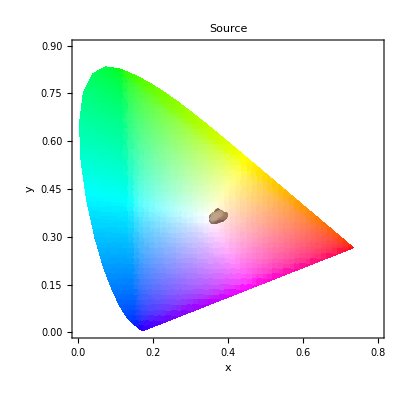

```mathematica
ChromaticityPlot[sourceRGBColor,MaxPlotPoints->Infinity,PlotLabel->"Source"]
```

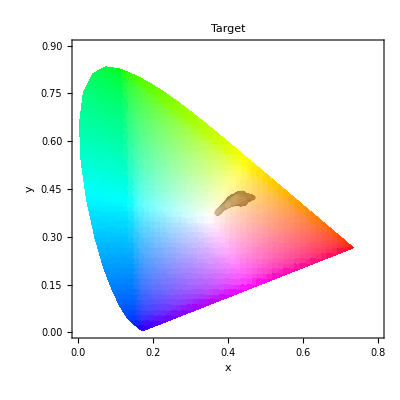

```mathematica
ChromaticityPlot[targetXYZColor,MaxPlotPoints->Infinity,PlotLabel->"Target"]
```

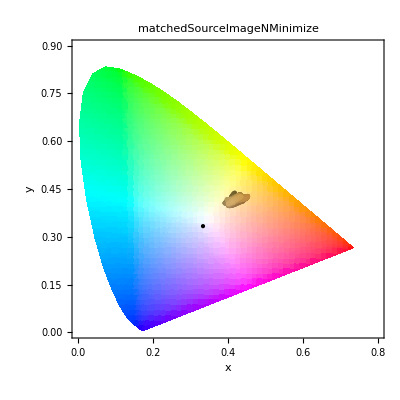

```mathematica
ChromaticityPlot[matchedSourceImageNMinimize,MaxPlotPoints->Infinity,PlotLabel->"matchedSourceImageNMinimize"]
```

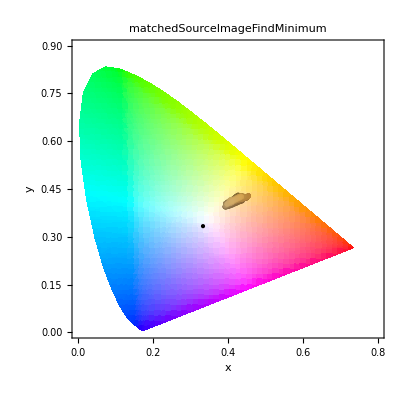

```mathematica
ChromaticityPlot[matchedSourceImageFindMinimum,MaxPlotPoints->Infinity,PlotLabel->"matchedSourceImageFindMinimum"]
```

#### ChromaticityPlot3D

```mathematica
ChromaticityPlot3D[srgbSourceImage
,MaxPlotPoints->Infinity
]
```

-Graphics3D-

```mathematica
ChromaticityPlot3D[srgbTargetImage
,MaxPlotPoints->Infinity
]
```

-Graphics3D-

```mathematica
ChromaticityPlot3D[matchedSourceImageNMinimize
,MaxPlotPoints->Infinity
]
```

-Graphics3D-

```mathematica
ChromaticityPlot3D[matchedSourceImageFindMinimum
,MaxPlotPoints->Infinity
]
```

-Graphics3D-

#### ListPointPlot3D

```mathematica
srgbSourceImageRGBVals=Pick[Flatten[ImageData[srgbSourceImage],1],maskAsIntsAll,1]; (* select source image pixels based on mask *)
```

```mathematica
srgbTargetImageRGBVals=Pick[Flatten[ImageData[srgbTargetImage],1],maskAsIntsAll,1]; (* select source image pixels based on mask *)
```

```mathematica
matchedSourceImageNMinimizeRGBVals=Pick[Flatten[ImageData[matchedSourceImageNMinimize],1],maskAsIntsAll,1]; (* select source image pixels based on mask *)
```

```mathematica
matchedSourceImageFindMinimumRGBVals=Pick[Flatten[ImageData[matchedSourceImageFindMinimum],1],maskAsIntsAll,1]; (* select source image pixels based on mask *)
```

```mathematica
Dimensions/@{srgbSourceImageRGBVals,srgbTargetImageRGBVals,matchedSourceImageNMinimizeRGBVals,matchedSourceImageFindMinimumRGBVals}
```

{{7455,3},{7455,3},{7455,3},{7455,3}}

```mathematica
ListPointPlot3D[{srgbSourceImageRGBVals,srgbTargetImageRGBVals}
,PlotLabel->"Source & Target",PlotRange->All,AxesLabel->{"R","G","B"},SphericalRegion->True,ImageSize->Large]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{srgbTargetImageRGBVals,matchedSourceImageNMinimizeRGBVals}
,PlotLabel->"Target & NMinimize",PlotRange->All,AxesLabel->{"R","G","B"},SphericalRegion->True,ImageSize->Large]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{srgbTargetImageRGBVals,matchedSourceImageFindMinimumRGBVals}
,PlotLabel->"Target & FindMinimum",PlotRange->All,AxesLabel->{"R","G","B"},SphericalRegion->True,ImageSize->Large]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{srgbTargetImageRGBVals,matchedSourceImageFindMinimumRGBVals}
,PlotLabel->"NMinimize & FindMinimum",PlotRange->All,AxesLabel->{"R","G","B"},SphericalRegion->True,ImageSize->Large]
```

-Graphics3D-

#### Stats

```mathematica
?stats
```

```mathematica
stats[Norm/@(matchedSourceImageNMinimizeRGBVals-srgbTargetImageRGBVals)]
```

{0.100925,0.0903721,0.120033,0.0649817,{0.00142127,0.505788},0.504366,7455}

```mathematica
stats[Norm/@(matchedSourceImageFindMinimumRGBVals-srgbTargetImageRGBVals)]
```

{0.104565,0.0943098,0.123997,0.0666483,{0.00160251,0.490995},0.489393,7455}

```mathematica
stats[Norm/@(matchedSourceImageFindMinimumRGBVals-matchedSourceImageNMinimizeRGBVals)]
```

{0.0220382,0.0189522,0.0270679,0.015717,{0.000429764,0.0958575},0.0954278,7455}

```mathematica
stats[Norm/@(srgbSourceImageRGBVals-srgbTargetImageRGBVals)]
```

{0.186203,0.179744,0.192835,0.0501429,{0.0600638,0.478682},0.418619,7455}

### Full Image Transform

```mathematica
ImageAssemble[{{linear2srgbImage[imgDefaultScaled],eqrBaseImgScaled}
,{colorTransform[imgDefaultScaled,rawToXYZIDTNMinimize],colorTransform[imgDefaultScaled,rawToXYZIDTFindMinimum]}}]
```

-Graphics-

## Epilogue

```mathematica
Now
```

Wed 4 May 2022 19:00:49GMT-7.